```mathematica
<<FeynCalc`
```

FeynCalc 10.2.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

## YXX → XX (Vector Portal)

```mathematica
(* Y(k1,mu) Xbar(k2) X(k3) -> Xbar(p1) X(p2) *)
(* 8 Feynman diagrams: 4 s-channel + 4 t-channel *)

FCClearScalarProducts[];

SP[k1,k1]=mY^2;SP[k2,k2]=mX^2;
SP[k3,k3]=mX^2;SP[p1,p1]=mX^2;SP[p2,p2]=mX^2;

SP[k1,k2]=(s12-mY^2-mX^2)/2;
SP[k1,k3]=(s13-mY^2-mX^2)/2;
SP[k1,p1]=(mY^2+mX^2-t1)/2;
SP[k2,p1]=(2 mX^2-t2)/2;
SP[k3,p1]=(2 mX^2-t3)/2;

(* k2.k3 from p2^2 = mX^2 *)
SP[k2,k3]=-(s12-mY^2-mX^2)/2-(s13-mY^2-mX^2)/2+(mY^2+mX^2-t1)/2+(2 mX^2-t2)/2+(2 mX^2-t3)/2-(mY^2+2 mX^2)/2;

(* p2 = k1+k2+k3-p1 cross terms *)
SP[p2,k1]=SP[k1,k1]+SP[k1,k2]+SP[k1,k3]-SP[k1,p1];
SP[p2,k2]=SP[k1,k2]+SP[k2,k2]+SP[k2,k3]-SP[k2,p1];
SP[p2,k3]=SP[k1,k3]+SP[k2,k3]+SP[k3,k3]-SP[k3,p1];
SP[p2,p1]=SP[k1,p1]+SP[k2,p1]+SP[k3,p1]-SP[p1,p1];

sqrtsNR=mY+2 mX;
sNR=sqrtsNR^2;
EXf=sqrtsNR/2;

NRrules={s12->(mY+mX)^2,s13->(mY+mX)^2,t1->mY^2+mX^2-2 mY EXf,t2->2 mX^2-2 mX EXf,t3->2 mX^2-2 mX EXf};

(* Internal Y propagator numerator *)
YProp[a_,b_,q_]:=-MT[a,b]+FV[q,a] FV[q,b]/mY^2;
```

```mathematica
(* S-CHANNEL diagrams: sign = +1 *)

(* S1: incoming s-channel, Y emitted from outgoing leg *)
qY1=k2+k3;
PX1=k2+k3-p1;
DenY1=ExpandScalarProduct[SP[qY1,qY1]]-mY^2;
DenX1=ExpandScalarProduct[SP[PX1,PX1]]-mX^2;
amp1=Contract[SpinorVBar[k2,mX].GA[al].SpinorU[k3,mX]*
YProp[al,be,qY1]*
SpinorUBar[p2,mX].GA[mu].(GS[PX1]+mX).GA[be].SpinorV[p1,mX]]/(DenY1 DenX1)//DiracSimplify;

(* S2: incoming s-channel, Y emitted from other outgoing leg *)
qY2=k2+k3;
PX2=k1-p1;
DenY2=ExpandScalarProduct[SP[qY2,qY2]]-mY^2;
DenX2=ExpandScalarProduct[SP[PX2,PX2]]-mX^2;
amp2=Contract[SpinorVBar[k2,mX].GA[al].SpinorU[k3,mX]*
YProp[al,be,qY2]*
SpinorUBar[p2,mX].GA[be].(GS[PX2]+mX).GA[mu].SpinorV[p1,mX]]/(DenY2 DenX2)//DiracSimplify;

(* S3: outgoing s-channel, Y absorbed by incoming X *)
qY3=p1+p2;
PX3=k1+k3;
DenY3=ExpandScalarProduct[SP[qY3,qY3]]-mY^2;
DenX3=ExpandScalarProduct[SP[PX3,PX3]]-mX^2;
amp3=Contract[SpinorVBar[k2,mX].GA[be].(GS[PX3]+mX).GA[mu].SpinorU[k3,mX]*
YProp[al,be,qY3]*
SpinorUBar[p2,mX].GA[al].SpinorV[p1,mX]]/(DenY3 DenX3)//DiracSimplify;

(* S4: outgoing s-channel, Y absorbed by incoming Xbar *)
qY4=p1+p2;
PX4=-(k1+k2);
DenY4=ExpandScalarProduct[SP[qY4,qY4]]-mY^2;
DenX4=ExpandScalarProduct[SP[PX4,PX4]]-mX^2;
amp4=Contract[SpinorVBar[k2,mX].GA[mu].(GS[PX4]+mX).GA[be].SpinorU[k3,mX]*
YProp[al,be,qY4]*
SpinorUBar[p2,mX].GA[al].SpinorV[p1,mX]]/(DenY4 DenX4)//DiracSimplify;

(* T-CHANNEL diagrams: sign = -1 (Fermi statistics) *)

(* T1: t-channel (k2-p1) *)
qY5=k2-p1;
PX5=k2+k3-p1;
DenY5=ExpandScalarProduct[SP[qY5,qY5]]-mY^2;
DenX5=ExpandScalarProduct[SP[PX5,PX5]]-mX^2;
amp5=Contract[SpinorVBar[k2,mX].GA[al].SpinorV[p1,mX]*
YProp[al,be,qY5]*
SpinorUBar[p2,mX].GA[mu].(GS[PX5]+mX).GA[be].SpinorU[k3,mX]]/(DenY5 DenX5)//DiracSimplify;

(* T2: t-channel (k3-p2) *)
qY6=k3-p2;
PX6=-(k1+k2);
DenY6=ExpandScalarProduct[SP[qY6,qY6]]-mY^2;
DenX6=ExpandScalarProduct[SP[PX6,PX6]]-mX^2;
amp6=Contract[SpinorUBar[p2,mX].GA[al].SpinorU[k3,mX]*
YProp[al,be,qY6]*
SpinorVBar[k2,mX].GA[mu].(GS[PX6]+mX).GA[be].SpinorV[p1,mX]]/(DenY6 DenX6)//DiracSimplify;

(* T3: t-channel (k3-p2), Y on other side *)
qY7=k3-p2;
PX7=k1+k3;
DenY7=ExpandScalarProduct[SP[qY7,qY7]]-mY^2;
DenX7=ExpandScalarProduct[SP[PX7,PX7]]-mX^2;
amp7=Contract[SpinorUBar[p2,mX].GA[be].(GS[PX7]+mX).GA[mu].SpinorU[k3,mX]*
YProp[al,be,qY7]*
SpinorVBar[k2,mX].GA[al].SpinorV[p1,mX]]/(DenY7 DenX7)//DiracSimplify;

(* T4: t-channel (k2-p1), Y on other side *)
qY8=k2-p1;
PX8=k1-p1;
DenY8=ExpandScalarProduct[SP[qY8,qY8]]-mY^2;
DenX8=ExpandScalarProduct[SP[PX8,PX8]]-mX^2;
amp8=Contract[SpinorVBar[k2,mX].GA[be].(GS[PX8]+mX).GA[mu].SpinorV[p1,mX]*
YProp[al,be,qY8]*
SpinorUBar[p2,mX].GA[al].SpinorU[k3,mX]]/(DenY8 DenX8)//DiracSimplify;

(* Collect all amplitudes; t-channel gets relative minus sign *)
amps={amp1,amp2,amp3,amp4,-amp5,-amp6,-amp7,-amp8};
```

```mathematica
(* Process one term: polarization sums as multiplicative tensors *)
proc[i_,j_]:=Module[{cc,Mij},cc=ComplexConjugate[amps⟦j⟧]/.{mu->mup};
Mij=FermionSpinSum[amps⟦i⟧ cc]*
(-MT[mu,mup]+FV[k1,mu] FV[k1,mup]/mY^2)//Contract//DiracSimplify;
Mij=Mij/.NRrules;
Mij=PowerExpand[Mij]/.mY->mX/r//FullSimplify];
```

```mathematica
outputDir=FileNameJoin[{NotebookDirectory[],"MsqTerms_YXX_XX_vP_v2"}];
If[!DirectoryQ[outputDir],CreateDirectory[outputDir]];
```

```mathematica
(* Diagonal terms *)
Do[Print["(",i,",",i,") ..."];
term=proc[i,i];
Put[term,FileNameJoin[{outputDir,"diag_"<>ToString[i]<>"_"<>ToString[i]<>".m"}]];
Clear[term];Print["  Done."];,{i,1,8}];

(* Off-diagonal terms (multiplied by 2) *)
Do[Print["(",i,",",j,") ..."];
term=2 proc[i,j];
Put[term,FileNameJoin[{outputDir,"offdiag_"<>ToString[i]<>"_"<>ToString[j]<>".m"}]];
Clear[term];Print["  Done."];,{i,1,8},{j,i+1,8}];

Print["\nAll 36 terms saved to: ",outputDir];
```

(1,1) ...

Done.

(2,2) ...

Done.

(3,3) ...

Done.

(4,4) ...

Done.

(5,5) ...

Done.

(6,6) ...

Done.

(7,7) ...

Done.

(8,8) ...

Done.

(1,2) ...

Done.

(1,3) ...

Done.

(1,4) ...

Done.

(1,5) ...

Done.

(1,6) ...

Done.

(1,7) ...

Done.

(1,8) ...

Done.

(2,3) ...

Done.

(2,4) ...

Done.

(2,5) ...

Done.

(2,6) ...

Done.

(2,7) ...

Done.

(2,8) ...

Done.

(3,4) ...

Done.

(3,5) ...

Done.

(3,6) ...

Done.

(3,7) ...

Done.

(3,8) ...

Done.

(4,5) ...

Done.

(4,6) ...

Done.

(4,7) ...

Done.

(4,8) ...

Done.

(5,6) ...

Done.

(5,7) ...

Done.

(5,8) ...

Done.

(6,7) ...

Done.

(6,8) ...

Done.

(7,8) ...

Done.

All 36 terms saved to: /home/gab/Desktop/PyCharm_env/secluded_DM/mathematica/MsqTerms_YXX_XX_vP_v2

## Load and sum

```mathematica
outputDir=FileNameJoin[{NotebookDirectory[],"MsqTerms_YXX_XX_vP_v2"}];
files=FileNames["*.m",outputDir];
Print["Loading ",Length[files]," terms..."];
MsqTotal=0;
Do[term=Get[f];MsqTotal+=term;Clear[term];,{f,files}];
MsqAvgNR=MsqTotal/12//Simplify;
```

Loading 36 terms...

```mathematica
MsqAvgNR//FullSimplify
```

```mathematica
sqrtsNR=mY+2 mX;
sNR=sqrtsNR^2;
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2 a b-2 a c-2 b c;
lambdaNR=Kallen[sNR,mX^2,mX^2]/.mY->mX/r//Simplify;

sigmav2NR=MsqAvgNR*Sqrt[lambdaNR]/(64 Pi mY mX^2 sNR);
sigmav2NR=(4 Pi alphaX)^3*sigmav2NR/.mY->mX/r//Simplify

Delta2=PowerExpand[sigmav2NR*mX^5/alphaX^3]//FullSimplify
```

(alphaX^3 π^2 r^5 √((mX^4 (1+2 r)^2 (1+4 r))/r^4) (31+196 r+326 r^2+56 r^3+152 r^4+1760 r^5-1280 r^6+1024 r^7))/(6 mX^7 (1+2 r)^4 (-1+r+2 r^2)^2)

(π^2 r^3 (1+4 r)^(3/2) (31+2 r (36+r (19+4 r (-12+r (67+16 r (-3+2 r)))))))/(6 (1+2 r)^3 (-1+r+2 r^2)^2)

```mathematica
N[Delta2/.r->1]
N[Delta2/.r->2]
N[Delta2/.r->10]
N[Delta2/.r->100]
```

77.1397

429.209

237915.

1.01554×10^9

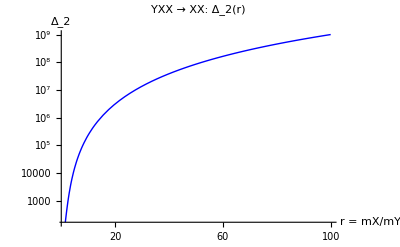

```mathematica
Plot[Delta2,{r,1.5,100},
PlotRange->All,
ScalingFunctions->{"Linear","Log"},
AxesLabel->{"r = mX/mY","Δ_2"},
PlotLabel->"YXX → XX:  Δ_2(r)",
PlotStyle->{Thick,Blue}]
```

```mathematica
Print["\n===== Delta_2(r) for selected mass ratios ====="];
Print[PaddedForm[
  TableForm[
   Table[{r0, N[Delta2 /. r -> r0, 8]}, {r0, {1.5,2, 3, 5, 7, 10, 15, 20, 50, 100}}],
   TableHeadings -> {None, {"r = mX/mY", "Delta_2"}}], {8, 4}]];
```

===== Delta_2(r) for selected mass ratios =====

r = mX/mY | Delta_2
    1.5000 |   167.9790
        2 |   429.2094
        3 |  2044.1905
        5 |  15928.6990
        7 |  60153.1970
       10 |  237915.4300
       15 |     1.0933×10^6
       20 |     3.1626×10^6
       50 |     8.6633×10^7
      100 |     1.0155×10^9

```mathematica
PowerExpand[(π^2 r^3 (1+4 r)^(3/2) (31+2 r (36+r (19+4 r (-12+r (67+16 r (-3+2 r)))))))/(6 (1+2 r)^3 (-1+r+2 r^2)^2)]/.r-> 1/rv//FullSimplify
```

(π^2 ((4+rv)/rv)^(3/2) (256+rv (-384+rv (536+rv (-96+rv (38+rv (72+31 rv)))))))/(6 rv^2 (2+rv)^3 (2+rv-rv^2)^2)